## <r^2(t)>, calcul numérique

### États propres dans la base atomique

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
ClearAll[A,v,r];
A[i_,v_,r_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_,v_,r_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->A[i,v,r],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* états propres et leurs énergies dans la base atomique *)
valvec[v_,r_,i_]:=Eigensystem[h[i,v,r]]
```

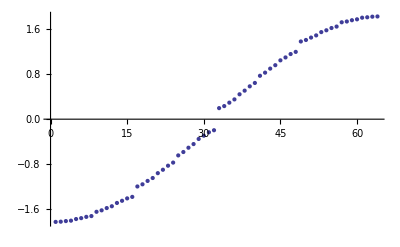

```mathematica
(* le spectre est bien comme on l'attend *)
ListPlot[Sort[valvec[.9,.9,6][[1]]]]
```

```mathematica
(* les vecteurs propres sont bien normalisés à 1 *)
Norm/@valvec[.1,.001,5][[2]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
(* attention ! on fixe les couplages et la taille du système ! *)
rmoy=Block[{n=7,v=.3,r=.3,val,vec,K,tmax=40,dt=.5,timelist,rmoy,d,dtot},
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
(* on place l'origine au bord gauche de la chaîne *)
dtot=Sum[A[i,v,r],{i,2^n}];
d=dtot^-1 ParallelTable[Sum[A[i,v,r],{i,j}],{j,2^n}];
{val,vec}=valvec[v,r,n];
timelist=Range[0,tmax,dt];
(* matrice K : propagateur *)
K=ParallelTable[Sum[Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[j]]],{k,2^n}],{t,timelist},{i,2^n},{j,2^n}];
(* diffusion : <r^2>_i = Subscript[Σ, j] (Subscript[d, j]-Subscript[d, i])^2 Subscript[(K^*), ji] Subscript[K, ji] *)
rmoy=Table[Sum[Abs[(d[[j]]-d[[i]])K[[timeIt,j,i]]]^2,{j,2^n}],{i,2^n},{timeIt,Length@timelist}]
];
```

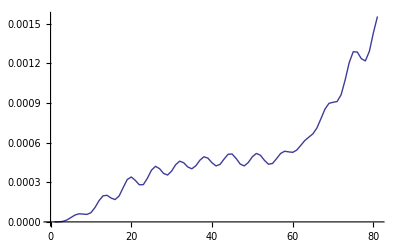

```mathematica
ListPlot[rmoy[[2^6]],Joined->True]
```

```mathematica
Sum[A[i,.3,.3],{i,2^7}]
```

75.2942

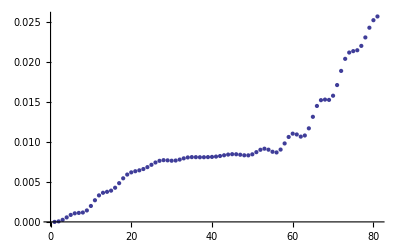

```mathematica
ListPlot[rmoy[[17]]]
```

```mathematica
(* attention ! on fixe les couplages et la taille du système ! *)
rper=Block[{n=7,v=1.,r=1.,val,vec,K,tmax=20,dt=.5,timelist,rmoy,d,dtot},
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
(* on place l'origine au bord gauche de la chaîne *)
dtot=Sum[A[i,v,r],{i,2^n}];
d=dtot^-1 ParallelTable[Sum[A[i,v,r],{i,j}],{j,2^n}];
{val,vec}=valvec[v,r,n];
timelist=Range[0,tmax,dt];
(* matrice K : propagateur *)
K=ParallelTable[Sum[Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[j]]],{k,2^n}],{t,timelist},{i,2^n},{j,2^n}];
(* diffusion : <r^2>_i = Subscript[Σ, j] (Subscript[d, j]-Subscript[d, i])^2 Subscript[(K^*), ji] Subscript[K, ji] *)
rmoy=Table[Sum[Abs[(d[[j]]-d[[i]])K[[timeIt,j,i]]]^2,{j,2^n}],{i,2^n},{timeIt,Length@timelist}]
];
```

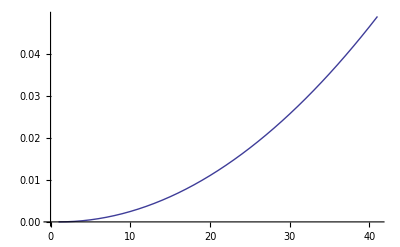

```mathematica
ListPlot[rper[[2^6]],Joined->True]
```